1.关于某一点可导性的问题：

1.1根据定义，某一点可导等效于该点函数割线斜率的左极限等于右极限。
考虑如下的函数：

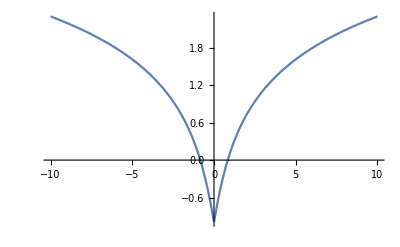

```mathematica
y[t_] :=log(√(t^2+1))+t tan^-1(1/t)-1

Plot[y[t],{t,-10,10}]
```

可以看到在x=0的位置，y[t]连续不可导。
考虑导函数：

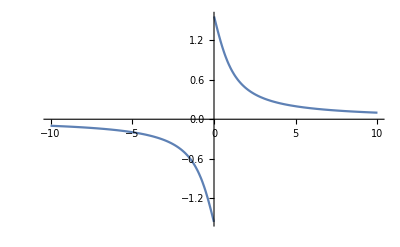

```mathematica
Plot[y'[t],{t,-10,10}]
```

导函数在x趋近于0时，为跳跃间断点，此时原函数一定不存在，也即原函数在x=0处不可导。
进而：不存在一个函数，它的割线左极限等于右极限，但是该点的导函数值不为该极限。因为根据定义，此极限所表示的正是导数值，所记忆的求导公式是根据定义推得的。
1.2一些常见的不定型

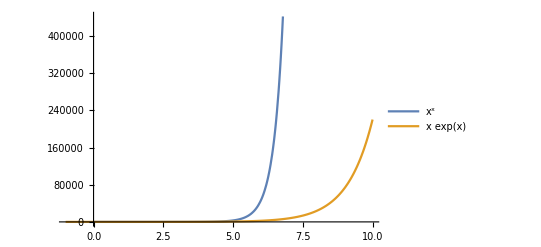

```mathematica
Plot[{x^x,x*Exp[x]},{x,-1,10},PlotLegends->LineLegend["Expressions"]]
```

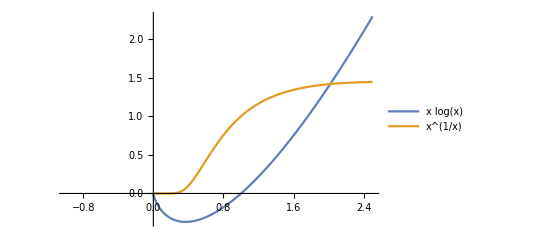

```mathematica
Plot[{x*Log[x],x^(1/x)},{x,-1,2.5},PlotLegends->LineLegend["Expressions"]]
```

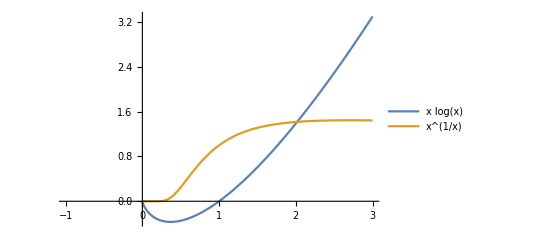

#### 2.关于反常积分敛散性的问题：

在定积分的定义中，函数可积代表函数有界，也即积分区域内不存在无穷间断点。
但是在反常积分中，定义被扩展，加入了无穷边界或无穷间断的定义，也即积分区域可能无穷或者存在无穷间断点。
此时反常积分的敛散性需要重新判断。
考虑如下的两个判别条件：

2.1无穷区间的反常积分

```mathematica
I1=∫_1^∞ 1/x^p ⅆx
```

当p<=1时，I1发散；
当p>1时，I1收敛。

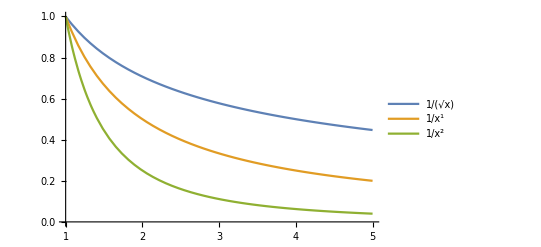

```mathematica
Plot[{1/(x^(1/2)),1/(x^1),1/(x^2)},{x,1,5},PlotLegends->LineLegend["Expressions"]]
```

可以直观看出，当x→∞，p>1更倾向于收敛，尽管区间无界，但是可积。

2.2无界函数的反常积分

```mathematica
I2=∫_0^1 1/x^p ⅆx
```

当p<1时，I2收敛；
当p>=1时，I2发散。

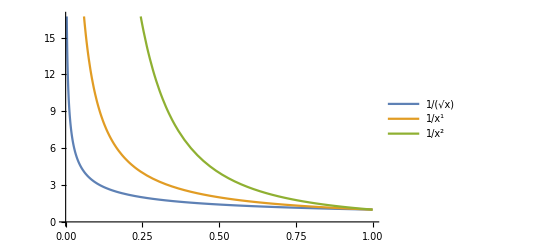

```mathematica
Plot[{1/(x^(1/2)),1/(x^1),1/(x^2)},{x,0,1},PlotLegends->LineLegend["Expressions"]]
```

可以直观看出，当x→0，p<1更倾向于收敛，尽管函数无界，但是可积。

2.3反常积分的敛散性与区间或被积函数的关系

根据以上，可以得出：

2.3.1	反常积分收敛推不出函数极限为0或有界

2.3.2函数极限为0推不出反常积分收敛
同理，函数极限为无穷推不出反常积分发散

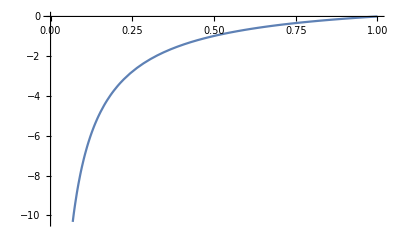

```mathematica
y(x_):=(log(x))/(√x);
Plot[y[x],{x,0,1}]
```

```mathematica
(log(x))/(√x)x0
```

Indeterminate

此时函数在x→1处极限不确定；

```mathematica
Integrate[y[x],{x,0,1}]
```

-4

但反常积分收敛。

故反常积分的敛散性不可通过被积函数在无穷或奇点的极限存在得知。具体判别可将被积函数等价转换为两种p函数的形式，进而判断敛散性。

2.4反常积分的万能判别公式
对于常见的反常积分，可以将其转化为如下的形式

```mathematica
∫_0^∞ 1/(x^a log^b(x))ⅆx
```

该反常积分上下限均为奇点，可将其拆为两个积分

```mathematica
∫_0^(1/2) 1/(x^a log^b(x))ⅆx+∫_(1/2)^2 1/(x^a log^b(x))ⅆx+∫_2^∞ 1/(x^a log^b(x))ⅆx
```

右侧积分：

```mathematica
{{{a>1}, {a=1,b>1}}收敛
```

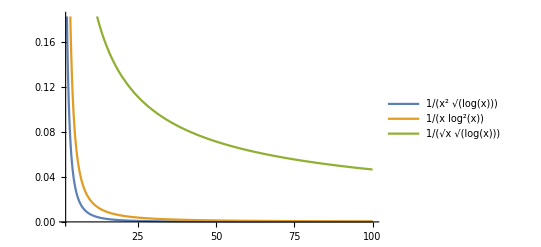

```mathematica
Plot[{1/(x^2*Log[x]^(1/2)),1/(x*Log[x]^(2)),1/(x^(1/2)*Log[x]^(1/2))},{x,2,100},PlotLegends->LineLegend["Expressions"]]
Integrate[{1/(x^2*Log[x]^(1/2)),1/(x*Log[x]^(2)),1/(x^(1/2)*Log[x]^(1/2))},{x,2,Infinity}]
```

左侧积分：

```mathematica
{{{a<1}, {a=1,b>1}}收敛
```

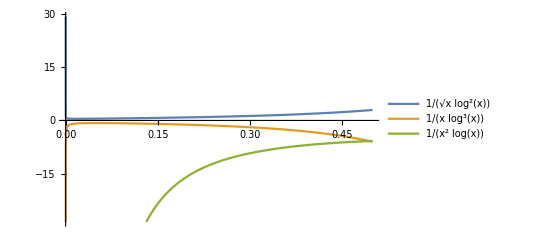

```mathematica
Plot[{1/(x^(1/2)*Log[x]^(2)),1/(x*Log[x]^(3)),1/(x^(2)*Log[x])},{x,0,1/2},PlotLegends->LineLegend["Expressions"]]
Integrate[{1/(x^(1/2)*Log[x]^(2)),1/(x*Log[x]^(3)),1/(x^(2)*Log[x])},{x,0,1/2}]
```

中间两个积分均发散：

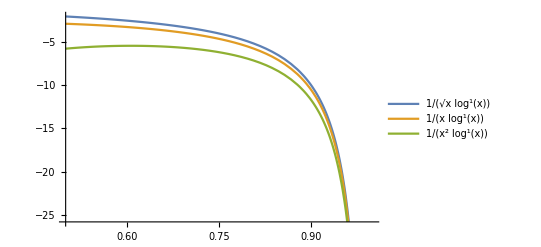

```mathematica
Plot[{1/(x^(1/2)*Log[x]^(1)),1/(x*Log[x]^(1)),1/(x^(2)*Log[x]^(1))},{x,1/2,1},PlotLegends->LineLegend["Expressions"]]
Integrate[{1/(x^(1/2)*Log[x]^(1)),1/(x*Log[x]^(1)),1/(x^(2)*Log[x])},{x,1/2,1}]
```

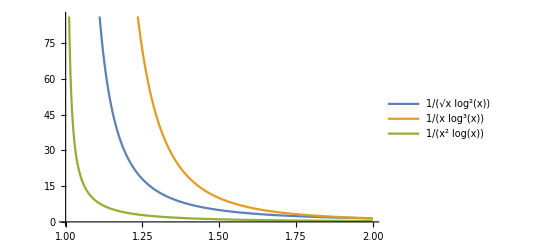

```mathematica
Plot[{1/(x^(1/2)*Log[x]^(2)),1/(x*Log[x]^(3)),1/(x^(2)*Log[x])},{x,1,2},PlotLegends->LineLegend["Expressions"]]
Integrate[{1/(x^(1/2)*Log[x]^(2)),1/(x*Log[x]^(3)),1/(x^(2)*Log[x])},{x,1,2}]
```

#### 3.关于一元函数连续，可导，导函数连续及驻点与拐点的问题

3.1函数连续
函数左极限等与右极限等于函数值
3.2函数可导
左侧割线斜率极限等于右侧（定义于开区间，当在闭区间求导是，导函数仅在开区间存在）
考虑如下问题：

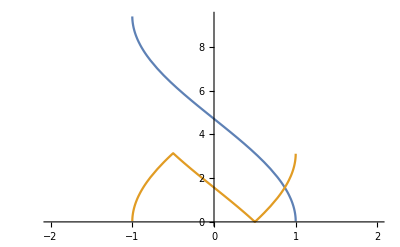

```mathematica
Plot[{3*ArcCos[x],ArcCos[3*x-4*x^3]},{x,-2,2}]
```

3.3由此两个简单的定义，衍生出许多问题：
3.3.1函数连续不一定可导，可导一定连续

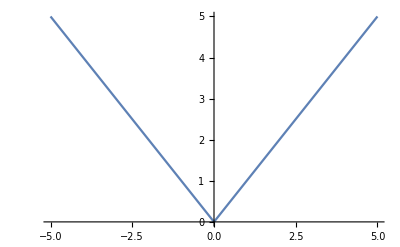

```mathematica
Plot[Abs[x],{x,-5,5}]
```

3.3.2函数可导则该点导函数值存在

3.3.3函数可导则导函数不会出现可去间断点、跳跃间断点、无穷间断点，可能存在振荡间断点

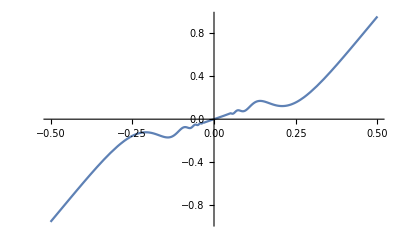

```mathematica
Plot[x+2*x^2*Sin[1/x],{x,-0.5,0.5}]
```

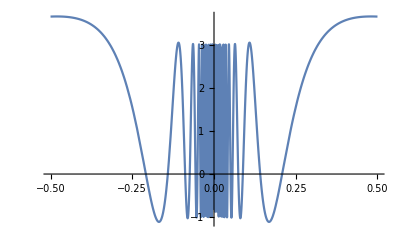

```mathematica
y[x_]:=x+2*x^2*Sin[1/x]
Plot[y'[x],{x,-0.5,0.5}]
```

3.3.4导函数连续则原函数可导，导函数不连续原函数不一定可导（考虑振荡间断点），也不一定连续

3.3.5导函数的单侧极限≠原函数的单侧导数；

```mathematica
lim_(x->Subscript[x, 0]) f'(x)≠lim_(x->Subscript[x, 0]) (f(x)−f(Subscript[x, 0]))/(x−Subscript[x, 0])
```

导函数双侧极限存在且相等推不出导函数在该点的值是否存在；

```mathematica
lim_(x->Subscript[x, 0]^+) f'(x)=lim_(x->Subscript[x, 0]^_) f'(x)=A{{{f'(x)=A，导函数连续，原函数可导}, {f'(x)≠A，无法确定}}
```

若导函数值存在，则原函数可导；若导函数值不存在，原函数不一定可导也不一定连续（考虑振荡间断点）。

3.3.6导函数可积，即含有有限个间断点，原函数不一定存在，具体看间断点的类型，自然原函数不一定连续、可导；
若导函数可积，则以导函数为被积函数的变上限积分一定连续。
若导函数连续，则一定存在原函数。

3.3.7若f’(x)在(a,b)连续，则考虑牛顿-莱布尼兹公式；
若f’(x)在(a,b)有界，则考虑拉格朗日公式。（此条件与拉格朗日条件等价）
（开区间有界定义为端点处极限存在）
结论：若f’(x)在(a,b)有界，f(x)有界
	      在无穷区间，若f’(x)与f(x)的有界性无关系

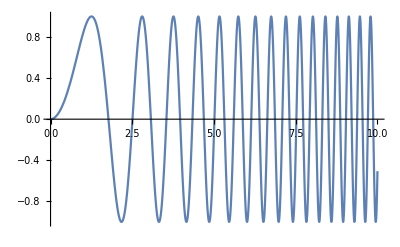

```mathematica
Plot[Sin[x^2],{x,0,10}]
```

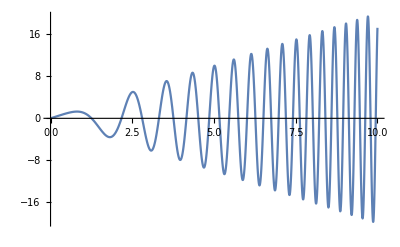

```mathematica
Plot[2*x*Cos[x^2],{x,0,10}]
```

3.4函数极值为在f(x)去心邻域内的最值
判断方法：
3.4.1在去心邻域内f’(x)变号（充分）
此判据依赖去心邻域而不关注该点的导函数是否存在

3.4.2若f’(x)=0,f’’(x)≠0；则该点为极值点（充分）
此判据关注导函数该点处的值，而不依赖去心邻域的性质
注意：当f’(x)=0,f’’(x)=0时，无法判断该点是否为极值点，并不能说明不为极值点
应用Lagrange中值定理和极限保号性判断。

3.5函数拐点为在f’(x)去心邻域内的最值
判断方法：
3.5.1在去心邻域内f’’(x)变号（充分）
可能包含奇点，奇点两侧区域正负无穷。  

3.5.2若f’’(x)=0,f’’’(x)≠0；则该点为拐点（充分）若全为0，则无法判断，不代表不为拐点

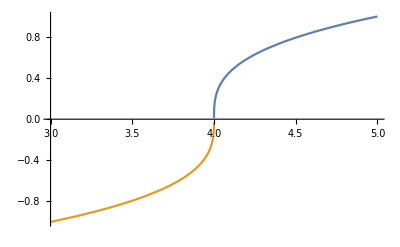

```mathematica
Plot[{(x-4)^(1/3),-(4-x)^(1/3)},{x,3,5}]
```

3.6衍生的问题：
3.6.1可以存在一点既是驻点又是拐点，但此时一阶不可导。即该点斜率存在突变。

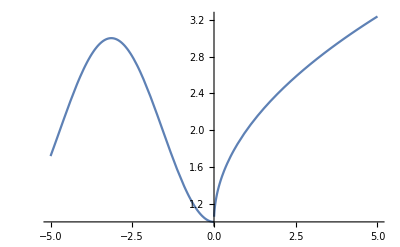

```mathematica
y[x_] := 2-Cos[x]/;x≤0
y[x_] := Sqrt[x]+1/;x>0
Plot[y[x],{x,-5,5}]
```

#### 4.多元函数的连续、可偏导、可微、偏导连续及极值问题

4.1连续

```mathematica
lim_{{x->Subscript[x, 0]}, {y->Subscript[y, 0]}} f(x,y)=f(Subscript[x, 0],Subscript[y, 0])
```

用于检验函数在某一点连续性，不考虑间断点类型
注意：x,y从任意方向趋近

4.2偏导存在（可偏导）

```mathematica
Subscript[f, x]'(Subscript[x, 0],Subscript[y, 0])=lim_(Δx->0) (f(Subscript[x, 0]+Δx,Subscript[y, 0])−f(Subscript[x, 0],Subscript[y, 0]))/Δx
Subscript[f, y]'(Subscript[x, 0],Subscript[y, 0])=lim_(Δy->0) (f(Subscript[x, 0],Subscript[y, 0]+Δy)−f(Subscript[x, 0],Subscript[y, 0]))/Δy
```

用于检验函数在某一点对x或y的偏导是否存在（仅代表x，y方向的偏导存在）

4.3可微

```mathematica
lim_{{Δx->0}, {Δy->0}} (Δz−(AΔx+BΔy))/(√(Δ x^2+Δ y^2))=0
```

极限存在，说明可微

4.4偏导的连续
利用偏导的定义求出某一点的偏导数，若函数的一阶偏导的极限与之相同，则连续

```mathematica
lim_{{x->Subscript[x, 0]}, {y->Subscript[y, 0]}} Subscript[f, x]'(x,y)=Subscript[f, x]'(Subscript[x, 0],Subscript[y, 0])
lim_{{x->Subscript[x, 0]}, {y->Subscript[y, 0]}} Subscript[f, y]'(x,y)=Subscript[f, y]'(Subscript[x, 0],Subscript[y, 0])
```

注意：此时的极限也是从任意方向趋近，而不是特定方向（要求任意方向偏导存在且等于该点偏导）

4.5衍生的问题：

4.5.1偏导连续可以推出函数可微，但是函数可微只可以推出偏导存在，此时偏导不一定连续（对于单个点讨论）
同时，若偏导存在，也不一定可微。

考虑函数可微但是偏导不连续的例子：

```mathematica
f(x_,y_):=(x^2+y^2) sin(1/(√(x^2+y^2)))
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

在x方向上，偏导数存在

```mathematica
dx=D[f[x,y],x]
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
Plot3D[dy,{x,-5,5},{y,-5,5}]
```

```mathematica
f[x_,y_]:=(x^2+y^2)*Sin[1/Sqrt[x^2+y^2]]
dy=D[f[x,y],y]
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
Plot3D[dy,{x,-5,5},{y,-5,5}]
```

考虑偏导存在但是函数不可微的例子：

```mathematica
Plot3D[x^2*y/(x^2+y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

4.5.2从某个方向的极限存在不能证明函数连续（包括原函数连续和导函数连续）

```mathematica
Plot3D[x^2*y/(x^4+y^2),{x,-5,5},{y,-5,5}]
```

-Graphics3D-

在x，y趋于0时，函数极限不存在，但在x方向上极限存在

4.5.3函数连续，偏导数不一定存在，函数不连续，偏导数可能存在（因为偏导仅代表x，y方向上的偏导数）

4.5.4函数连续不一定可微，函数可微一定连续，不连续一定不可微。

4.5.5关于可微的证明：
4.5.5.1已知另一极限存在，证明可微性：
需要证明函数偏导存在，且定义式为0

```mathematica
Subscript[f, x]'(Subscript[x, 0],Subscript[y, 0])=lim_(Δx->0) (f(Subscript[x, 0]+Δx,Subscript[y, 0])−f(Subscript[x, 0],Subscript[y, 0]))/Δx
Subscript[f, y]'(Subscript[x, 0],Subscript[y, 0])=lim_(Δy->0) (f(Subscript[x, 0],Subscript[y, 0]+Δy)−f(Subscript[x, 0],Subscript[y, 0]))/Δy
且：lim_{{Δx->0}, {Δy->0}} (Δz−(AΔx+BΔy))/(√(Δ x^2+Δ y^2))=0
```

4.5.5.2已知可微，证明另一极限存在
根据可微可以得出：定义式为0，并由定义式变换为极限的结构证明

```mathematica
即：f(x,y)=f(Subscript[x, 0],Subscript[y, 0])+(AΔx+BΔy)+∘(ρ)
```

或直接证明z的变化量与全微分的差值为高阶无穷小

4.5.6求多元函数极限的思路：

4.5.6.1去路径反证极限不存在

4.5.6.2不等式比较收敛

4.5.6.3加绝对值比较，绝对值极限存在，原极限一定存在，相差一个正负号。

4.6极值问题

4.6.1极值的判定：
4.6.1.1无条件极值的判定：
严格按照步骤，一阶导等于0，且二阶导的判别式大于0，此时A大于0，为极小值；A小于0为极大值。
4.6.1.2条件极值的判定:
拉格朗日乘数法：
通过构造函数的一阶偏导均为0，解出所有的可疑点，进行判断极值。
可疑点包括：区域内部存在的驻点和通过构造函数在区域边界取得的可能的极值点。

4.6.2衍生的问题
4.6.2.1极值点不一定是拐点，拐点也不一定是极值点。（极值点为去心邻域内的性质，与该点存在与否无关，而拐点只表明偏导为0，不能体现符号相反。）
4.6.2.2对于一元函数，有界闭区域D内唯一极值一定为最值；但对于多元函数，由于极值为某一去心邻域内任意方向的最值，可能存在某一方向下降，另一方向上升的情况，此时虽然函数可以减小，但是不为极小值点，也即，函数可以不通过极小值点而先降低再升高，此时极值点仍然唯一，但是函数会上升。
考虑马鞍面的特例：

```mathematica
ContourPlot3D[x^3-4*x^2+x*y-y^2==z,{x,-3,6},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

#### 5.关于积分比较问题的思路

此类题目一般为函数在积分区间上恒大于的问题。
5.1画图比较积分区域面积的大小：
考虑下题：

```mathematica
Subscript[I, k]=∫_0^(π k) exp(x^2) sin(x)ⅆx
```

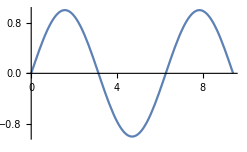
-Graphics- -Graphics-

```mathematica
Plot[{Exp[x^2]},{x,0,3*Pi}]                            Plot[Sin[x],{x,0,3*Pi}]
```

显然 I_3>I_1>I_2